### Perceptron Convergence Theorem-Numerical Illustration

We work in ℝ.b2 and construct data that is linearly separable by a "teacher" hyperplane (w^*,b^*).

```mathematica
ClearAll[generateSeparableData]
```

```mathematica
generateSeparableData[nSamples_,dim_,margin_]:=Module[{wStar,bStar,x,m,label,X={},y={}},(*Random but fixed separator*)wStar=Normalize[RandomReal[NormalDistribution[0,1],dim]];
bStar=RandomReal[NormalDistribution[0,0.1]];
While[Length[X]<nSamples,x=RandomVariate[NormalDistribution[0,1],dim];
m=wStar.x+bStar;
If[Abs[m]<margin,Continue[]];
label=If[m>0,1,-1];
AppendTo[X,x];
AppendTo[y,label];];
<|"X"->X,"y"->y,"wStar"->wStar,"bStar"->bStar|>]
```

```mathematica
data=generateSeparableData[60, 2, 0.01]
```

<|X→{{0.249334,-1.13311},{-0.608842,-1.6313},{-0.583875,-0.183894},{0.788876,0.311926},{0.674122,-1.35311},{-1.39333,-0.310924},{0.911679,-0.186661},{-0.381773,-0.260198},{-0.051436,0.141476},{-0.256701,-1.51856},{-0.655449,1.35051},{-1.30726,0.680499},{-0.329172,-0.902252},{-0.241739,0.240388},{-0.787827,0.319604},{-0.342625,1.05775},{0.33018,-2.2407},{0.063146,0.170597},{-1.56693,-1.58887},{-1.23681,-0.611086},{0.774065,1.52022},{-0.117869,1.46047},{-0.232091,1.10023},{0.615981,-2.84505},{-1.37428,-0.403954},{-1.19532,0.579547},{0.782907,-0.331854},{0.904582,0.957991},{1.02436,-0.297771},{1.419,-0.196001},{-0.315283,-1.16479},{0.1668,0.790905},{1.09682,0.0996373},{0.179655,-1.31645},{-0.677519,0.0278771},{-0.0899046,1.08644},{2.7171,0.30213},{0.167918,0.580165},{-0.170277,0.304542},{0.733948,-1.42656},{1.11088,0.654935},{0.491511,-1.01011},{-0.0363295,-0.615061},{0.262571,0.438612},{-0.675055,1.23667},{0.206511,-0.519051},{0.197743,1.5819},{-1.2968,-2.22199},{-0.38051,0.134161},{-0.339336,-1.63332},{1.77593,0.469068},{1.66424,0.308808},{-0.16415,-1.21688},{1.18555,-0.313483},{1.74789,-0.176835},{1.54578,0.588618},{-0.181552,0.518609},{-0.332239,0.151707},{-1.35165,-0.451836},{0.0297235,-2.37345}},y→{-1,-1,1,-1,-1,1,-1,1,1,-1,1,1,-1,1,1,1,-1,1,1,1,1,1,1,-1,1,1,-1,-1,-1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,-1,-1,1,1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1},wStar→{-0.804466,0.593999},bStar→0.0587749|>

```mathematica
X=data["X"]
```

{{0.249334,-1.13311},{-0.608842,-1.6313},{-0.583875,-0.183894},{0.788876,0.311926},{0.674122,-1.35311},{-1.39333,-0.310924},{0.911679,-0.186661},{-0.381773,-0.260198},{-0.051436,0.141476},{-0.256701,-1.51856},{-0.655449,1.35051},{-1.30726,0.680499},{-0.329172,-0.902252},{-0.241739,0.240388},{-0.787827,0.319604},{-0.342625,1.05775},{0.33018,-2.2407},{0.063146,0.170597},{-1.56693,-1.58887},{-1.23681,-0.611086},{0.774065,1.52022},{-0.117869,1.46047},{-0.232091,1.10023},{0.615981,-2.84505},{-1.37428,-0.403954},{-1.19532,0.579547},{0.782907,-0.331854},{0.904582,0.957991},{1.02436,-0.297771},{1.419,-0.196001},{-0.315283,-1.16479},{0.1668,0.790905},{1.09682,0.0996373},{0.179655,-1.31645},{-0.677519,0.0278771},{-0.0899046,1.08644},{2.7171,0.30213},{0.167918,0.580165},{-0.170277,0.304542},{0.733948,-1.42656},{1.11088,0.654935},{0.491511,-1.01011},{-0.0363295,-0.615061},{0.262571,0.438612},{-0.675055,1.23667},{0.206511,-0.519051},{0.197743,1.5819},{-1.2968,-2.22199},{-0.38051,0.134161},{-0.339336,-1.63332},{1.77593,0.469068},{1.66424,0.308808},{-0.16415,-1.21688},{1.18555,-0.313483},{1.74789,-0.176835},{1.54578,0.588618},{-0.181552,0.518609},{-0.332239,0.151707},{-1.35165,-0.451836},{0.0297235,-2.37345}}

```mathematica
y=data["y"]
```

{-1,-1,1,-1,-1,1,-1,1,1,-1,1,1,-1,1,1,1,-1,1,1,1,1,1,1,-1,1,1,-1,-1,-1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,-1,-1,1,1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1}

```mathematica
wStar=data["wStar"]
```

{-0.804466,0.593999}

```mathematica
bStar=data["bStar"]
```

0.0587749

```mathematica
Dimensions[X]
```

{60,2}

```mathematica
Counts[y]
```

<|-1→31,1→29|>

### Plot of linearly separable data

```mathematica
pos = Pick[X, UnitStep[y], 1]
```

{{-0.583875,-0.183894},{-1.39333,-0.310924},{-0.381773,-0.260198},{-0.051436,0.141476},{-0.655449,1.35051},{-1.30726,0.680499},{-0.241739,0.240388},{-0.787827,0.319604},{-0.342625,1.05775},{0.063146,0.170597},{-1.56693,-1.58887},{-1.23681,-0.611086},{0.774065,1.52022},{-0.117869,1.46047},{-0.232091,1.10023},{-1.37428,-0.403954},{-1.19532,0.579547},{0.1668,0.790905},{-0.677519,0.0278771},{-0.0899046,1.08644},{0.167918,0.580165},{-0.170277,0.304542},{0.262571,0.438612},{-0.675055,1.23667},{0.197743,1.5819},{-0.38051,0.134161},{-0.181552,0.518609},{-0.332239,0.151707},{-1.35165,-0.451836}}

```mathematica
neg = Pick[X, UnitStep[-y], 1]
```

{{0.249334,-1.13311},{-0.608842,-1.6313},{0.788876,0.311926},{0.674122,-1.35311},{0.911679,-0.186661},{-0.256701,-1.51856},{-0.329172,-0.902252},{0.33018,-2.2407},{0.615981,-2.84505},{0.782907,-0.331854},{0.904582,0.957991},{1.02436,-0.297771},{1.419,-0.196001},{-0.315283,-1.16479},{1.09682,0.0996373},{0.179655,-1.31645},{2.7171,0.30213},{0.733948,-1.42656},{1.11088,0.654935},{0.491511,-1.01011},{-0.0363295,-0.615061},{0.206511,-0.519051},{-1.2968,-2.22199},{-0.339336,-1.63332},{1.77593,0.469068},{1.66424,0.308808},{-0.16415,-1.21688},{1.18555,-0.313483},{1.74789,-0.176835},{1.54578,0.588618},{0.0297235,-2.37345}}

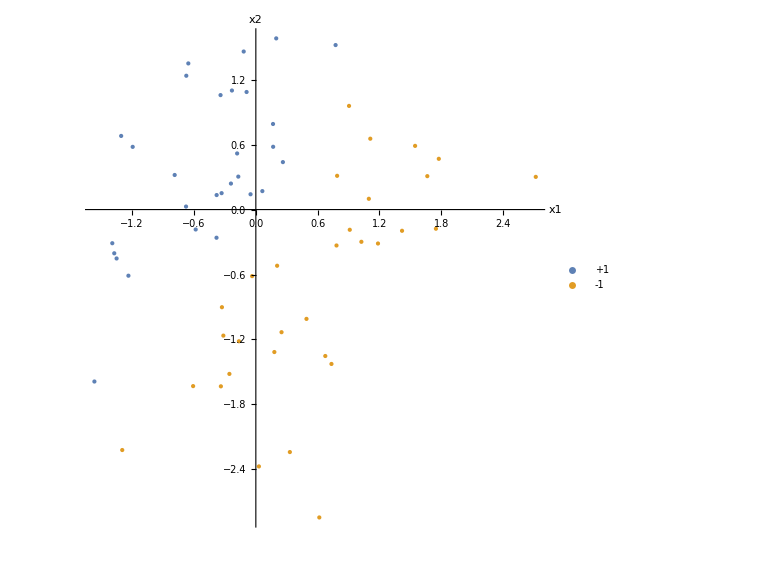

```mathematica
ListPlot[
 {
  pos,
  neg
 },
 PlotStyle -> {PointSize[Large], PointSize[Large]},
 PlotLegends -> {"+1", "-1"},
 AxesLabel -> {"x1", "x2"},
 PlotRange -> All,
 ImageSize -> Large,
 AspectRatio -> 1
]
```

### Perceptron algorithm with tracking

```mathematica
ClearAll[perceptronTrain]
```

```mathematica
perceptronTrain[X_List, y_List, maxEpochs_Integer : 1000, wStar_: None, bStar_: None] :=
 Module[{nSamples, dim, w, b, epoch, i, xi, yi, margin, mistakes,
   historyW = {}, historyB = {}, historyWDotWStar = {}, historyWNormSq = {},
   mistakesPerEpoch = {}, totalUpdates = 0, wDot},

  nSamples = Length[X];
  dim = Length[First[X]];
  w = ConstantArray[0., dim];
  b = 0.;

  For[epoch = 1, epoch <= maxEpochs, epoch++,
   mistakes = 0;
   For[i = 1, i <= nSamples, i++,
    xi = X[[i]];
    yi = y[[i]];
    margin = yi (w . xi + b);
    If[margin <= 0,
     w = w + yi xi;
     b = b + yi;
     mistakes++;
     totalUpdates++;

     If[wStar =!= None,
      wDot = w . wStar;
      AppendTo[historyWDotWStar, wDot];
      ,
      AppendTo[historyWDotWStar, Missing["NotAvailable"]];
     ];
     AppendTo[historyWNormSq, w . w];
     AppendTo[historyW, w];
     AppendTo[historyB, b];
    ];
   ];
   AppendTo[mistakesPerEpoch, mistakes];
   If[mistakes == 0, Break[]];
  ];

  <|
   "wFinal" -> w,
   "bFinal" -> b,
   "historyW" -> historyW,
   "historyB" -> historyB,
   "historyWDotWStar" -> historyWDotWStar,
   "historyWNormSq" -> historyWNormSq,
   "mistakesPerEpoch" -> mistakesPerEpoch,
   "totalUpdates" -> totalUpdates
  |>
 ]
```

```mathematica
result = perceptronTrain[X, y, 100, wStar, bStar]
```

<|wFinal→{-3.47586,2.51536},bFinal→0.,historyW→{{-0.249334,1.13311},{-0.83321,0.94922},{-2.40014,-0.639654},{-1.62608,0.880568},{-2.40898,1.21242},{-2.0937,2.37721},{-3.66063,0.788338},{-2.88657,2.30856},{-3.79115,1.35057},{-3.47586,2.51536}},historyB→{-1.,0.,1.,2.,1.,0.,1.,2.,1.,0.},historyWDotWStar→{0.87365,1.23412,1.55088,1.83118,2.65812,3.09637,3.41312,3.69343,3.85209,4.29033},historyWNormSq→{1.34612,1.59526,6.16983,3.41952,7.27316,10.0347,14.0217,13.6617,16.1968,18.4087},mistakesPerEpoch→{6,4,0},totalUpdates→10|>

```mathematica
wFinal = result["wFinal"]
```

{-3.47586,2.51536}

```mathematica
bFinal = result["bFinal"]
```

0.

```mathematica
totalUpdates = result["totalUpdates"]
```

10

```mathematica
mistakesPerEpoch = result["mistakesPerEpoch"]
```

{6,4,0}

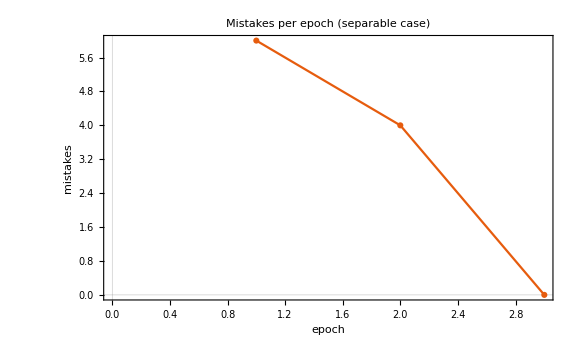

```mathematica
ListLinePlot[
 mistakesPerEpoch,
 AxesLabel -> {"epoch", "mistakes"},
 PlotMarkers -> Automatic,
 PlotTheme -> "Scientific",
 ImageSize -> Large,
 PlotLabel -> "Mistakes per epoch (separable case)"
]
```

### Decision boundary in ℝ^2

```mathematica
ClearAll[plotDecisionBoundary]
```

```mathematica
plotDecisionBoundary[w_, b_, X_, y_] :=
 Module[{pos, neg, line},
  pos = Pick[X, UnitStep[y], 1];
  neg = Pick[X, UnitStep[-y], 1];

  Show[
   ListPlot[
    {pos, neg},
    PlotStyle -> {PointSize[Large], PointSize[Large]},
    PlotLegends -> {"+1", "-1"},
    AxesLabel -> {"x1", "x2"},
    PlotRange -> All,
    AspectRatio -> 1
   ],
   (* line w.x + b == 0 => x2 = -(w1 x1 + b)/w2 *)
   If[w[[2]] != 0,
    line = Plot[
      -(w[[1]] x + b)/w[[2]],
      {x, Min[X[[All, 1]]] - 1, Max[X[[All, 1]]] + 1}
     ];
    line,
    {}
   ],
   ImageSize -> Large,
   PlotLabel -> "Perceptron decision boundary"
  ]
 ]
```

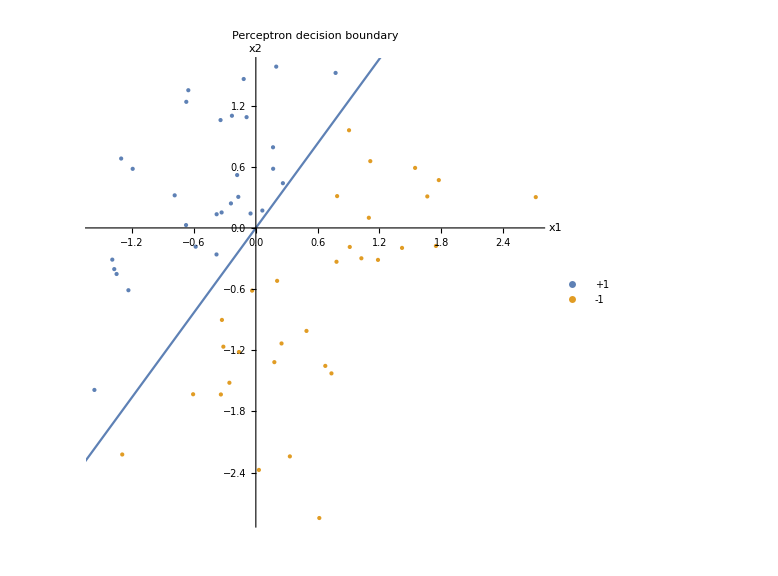

```mathematica
plotDecisionBoundary[wFinal, bFinal, X, y]
```

### R, gamma, and theoretical bound

```mathematica
norms = Norm /@ X
```

{1.16022,1.74121,0.61215,0.848306,1.51174,1.4276,0.930592,0.462011,0.150536,1.5401,1.50116,1.47378,0.960424,0.340916,0.850187,1.11186,2.26489,0.181908,2.23155,1.37953,1.70595,1.46521,1.12444,2.91097,1.43242,1.32841,0.850335,1.31758,1.06676,1.43247,1.20671,0.808303,1.10133,1.32865,0.678093,1.09015,2.73384,0.603977,0.348912,1.60429,1.28957,1.12334,0.616133,0.511199,1.40892,0.558624,1.59422,2.57273,0.403468,1.66819,1.83683,1.69264,1.2279,1.22629,1.75681,1.65406,0.549469,0.365236,1.42517,2.37364}

```mathematica
R = Max[norms]
```

2.91097

```mathematica
marginsTeacher = MapThread[#1 (#2 . wStar + bStar) &, {y, X}]
```

{0.814875,0.420422,0.41925,0.390565,1.28728,0.994976,0.785516,0.211341,0.18419,0.636738,1.38826,1.51464,0.212354,0.396036,0.882399,0.962708,1.53781,0.10931,0.375528,0.690758,0.339076,1.02111,0.89902,2.12672,0.924387,1.36462,0.768168,0.0998851,0.942164,1.19918,0.379474,0.394387,0.764392,0.867722,0.620375,0.776444,1.94757,0.268308,0.376654,1.37903,0.445856,0.936631,0.277345,0.10808,1.33641,0.415672,0.839346,0.217858,0.444574,0.638428,1.09127,1.09661,0.531999,1.08117,1.45238,0.835115,0.51288,0.416163,0.877742,1.37496}

```mathematica
gamma = Min[marginsTeacher]
```

0.0998851

```mathematica
bound = If[gamma > 0, (R/gamma)^2, Infinity]
<|"R" -> R, "gamma" -> gamma, "bound" -> bound, "observedUpdates" -> totalUpdates|>
```

849.324

<|R→2.91097,gamma→0.0998851,bound→849.324,observedUpdates→10|>

```mathematica
wDotWStar = DeleteMissing[result["historyWDotWStar"]]
```

{0.87365,1.23412,1.55088,1.83118,2.65812,3.09637,3.41312,3.69343,3.85209,4.29033}

```mathematica
wNormSq = result["historyWNormSq"]
```

{1.34612,1.59526,6.16983,3.41952,7.27316,10.0347,14.0217,13.6617,16.1968,18.4087}

```mathematica
steps = Range[Length[wNormSq]]
```

{1,2,3,4,5,6,7,8,9,10}

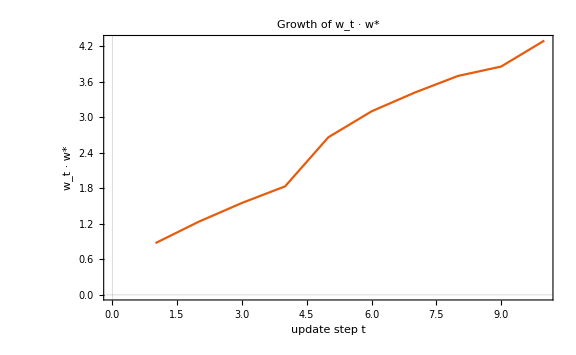

```mathematica
ListLinePlot[
 wDotWStar,
 AxesLabel -> {"update step t", "w_t · w*"},
 PlotTheme -> "Scientific",
 PlotLabel -> "Growth of w_t · w*",
 ImageSize -> Large
]
```

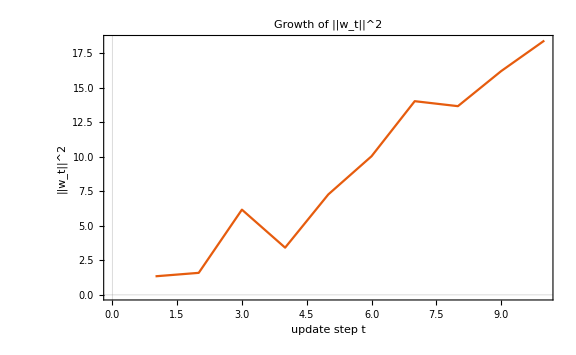

```mathematica
ListLinePlot[
 wNormSq,
 AxesLabel -> {"update step t", "||w_t||^2"},
 PlotTheme -> "Scientific",
 PlotLabel -> "Growth of ||w_t||^2",
 ImageSize -> Large
]
```

## Non-separable data: XOR

```mathematica
Xxor = {
  {1., 1.},
  {1., -1.},
  {-1., 1.},
  {-1., -1.}
}
```

{{1.,1.},{1.,-1.},{-1.,1.},{-1.,-1.}}

```mathematica
yxor = {1, -1, -1, 1}
```

{1,-1,-1,1}

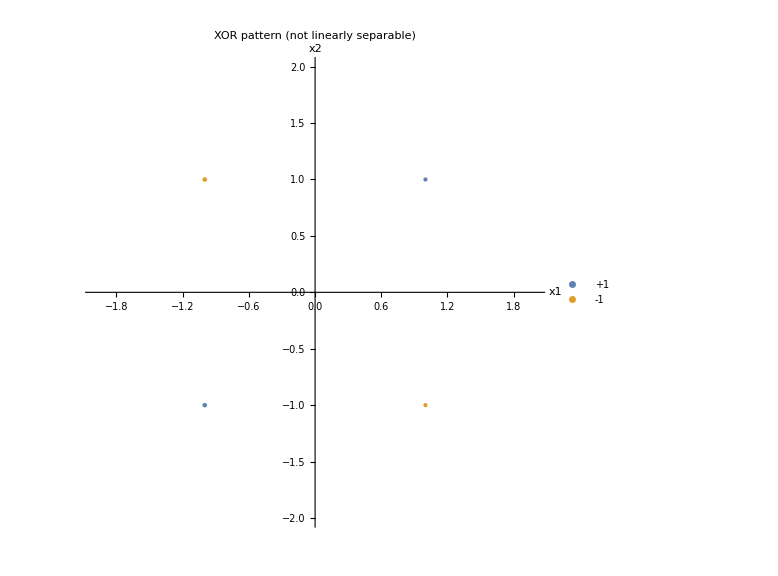

```mathematica
ListPlot[
 {
  Pick[Xxor, UnitStep[yxor], 1],
  Pick[Xxor, UnitStep[-yxor], 1]
 },
 PlotStyle -> {PointSize[Large], PointSize[Large]},
 PlotLegends -> {"+1", "-1"},
 AxesLabel -> {"x1", "x2"},
 PlotRange -> {{-2, 2}, {-2, 2}},
 PlotLabel -> "XOR pattern (not linearly separable)",
 ImageSize -> Large,
 AspectRatio -> 1
]
```

```mathematica
resultXor = perceptronTrain[Xxor, yxor, 50]
```

<|wFinal→{0.,0.},bFinal→0.,historyW→{{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.}},historyB→{1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.},historyWDotWStar→{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]},historyWNormSq→{2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.},mistakesPerEpoch→{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},totalUpdates→200|>

```mathematica
wXor = resultXor["wFinal"]
```

{0.,0.}

```mathematica
bXor = resultXor["bFinal"]
```

0.

```mathematica
mistakesXor = resultXor["mistakesPerEpoch"]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
totalUpdatesXor = resultXor["totalUpdates"]
```

200

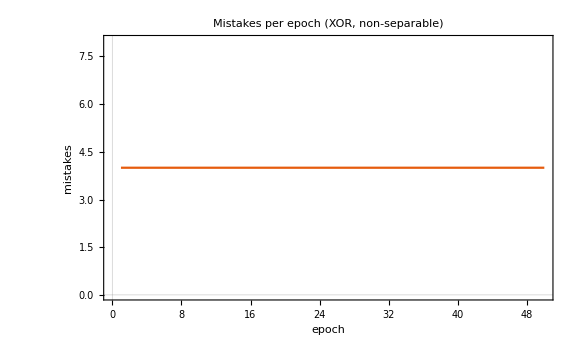

```mathematica
ListLinePlot[
 mistakesXor,
 AxesLabel -> {"epoch", "mistakes"},
 PlotTheme -> "Scientific",
 PlotLabel -> "Mistakes per epoch (XOR, non-separable)",
 ImageSize -> Large
]
```

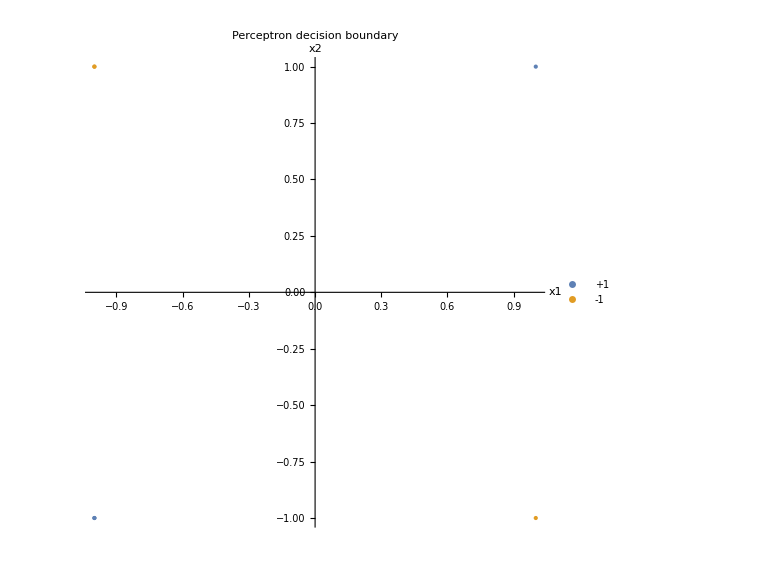

```mathematica
plotDecisionBoundary[wXor, bXor, Xxor, yxor]
```